# Muon Production in SM - γ-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
Quit[]
```

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="A-mm-SM";
```

```mathematica
SetOptions[InsertFields,Model->"SM",GenericModel->"Lorentz",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{4,5}];
```

## Tree-Level

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

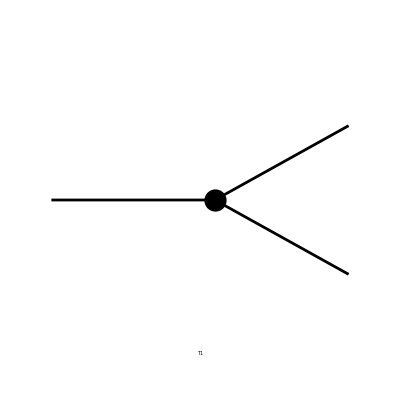

```mathematica
tops=CreateTopologies[0,1->2,Adjacencies->3];
Paint[tops];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

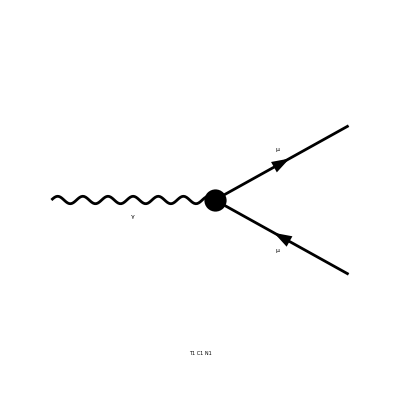

```mathematica
ins=InsertFields[tops, process];
Paint[ins];
```

## Feynman Amplitudes

```mathematica
amp=CreateFeynAmp[ins,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

## FormCalc results

```mathematica
ClearProcess[]
```

```mathematica
result=CalcFeynAmp[amp]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL (F1+F2)]

```mathematica
UVDivergentPart[result]
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]

## One-Loop

## Topologies

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

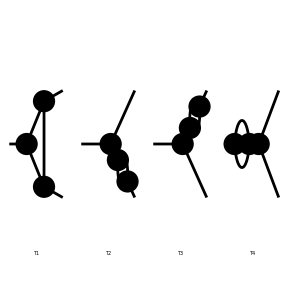

```mathematica
tops1=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[tops1];
```

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

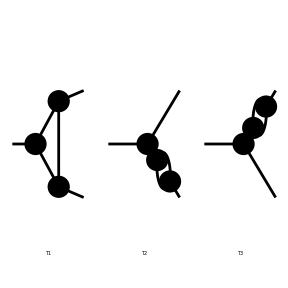

```mathematica
tops1=Delete[tops1,4];
Paint[tops1];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 3 Generic, 3 Classes, 3 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

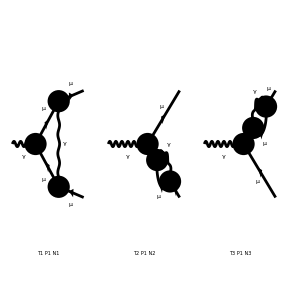

```mathematica
ins1=InsertFields[tops1, process,QEDOnly];
Paint[ins1, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[q1],-1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).(MM+gs[q1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[q1-k1-k2]).(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).v[k2,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(q1-k1)^2,1/(-MM2+(q1-k1-k2)^2)] g[Lor2,Lor3] ep[V[1],p1,Lor1]],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==2],Integral[q1],-1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[-(k2)]).(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).(MM+gs[q1]).(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(q1+k2)^2] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-MM2+(k2)^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==1,Number==3],Integral[q1],-1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).(MM+gs[-(q1)]).(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).(MM+gs[k1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(q1+k1)^2] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-MM2+(k1)^2)]]

## FormCalc results

```mathematica
result1=CalcFeynAmp[amp1]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/π Alfa EL (-Sub1 (C0i[cc1,MM2,0,MM2,0,MM2,MM2]+C0i[cc2,MM2,0,MM2,0,MM2,MM2])+(F3+F4) MM Pair1 (C0i[cc11,MM2,0,MM2,0,MM2,MM2]+2 C0i[cc12,MM2,0,MM2,0,MM2,MM2]+C0i[cc22,MM2,0,MM2,0,MM2,MM2])+(F1+F2) (Finite/4-1/2 B0i[bb0,MM2,0,MM2]+C0i[cc00,MM2,0,MM2,0,MM2,MM2]+MM2 (-C0i[cc0,MM2,0,MM2,0,MM2,MM2]+(Finite-2 B0i[bb0,MM2,0,MM2]+2 B0i[bb1,MM2,0,MM2]) Den[MM2,MM2])))]

```mathematica
uvResult1=UVDivergentPart[result1]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa EL (F1+F2) (Divergence+12 Divergence MM2 Den[MM2,MM2]))/(4 π)]

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
selectFeynAmp[amp_,i_Integer/;i≥0]:=amp[[0]][amp[[i]]]
```

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#]]&,amp]
```

```mathematica
replacement={PolarizationVector[V[1],FourMomentum[Incoming,1],Index[Lorentz,i_Integer]]->FourVector[FourMomentum[Incoming,1],Index[Lorentz,i]]}
```

{ep[V[1],p1,Lori_Integer]→(p1)[Lori]}

## Computations

```mathematica
result1List=calcFeynAmpList[amp1]/.result1List[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDiv=Map[UVDivergentPart,result1List]//Simplify
```

{Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2))/(4 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)]}

```mathematica
uvDivL=Map[#[[1]]&,uvDiv]/.uvDiv[[0]]->List
```

{-(Alfa Divergence EL (F1+F2))/(4 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)}

## CounterTerms

## CT Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

> Top. 2 ad/bdce/ed.m, 0 diagrams

> Top. 3 ad/becd/ed.m, 0 diagrams

> Top. 4 ad/bece/de.m, 0 diagrams

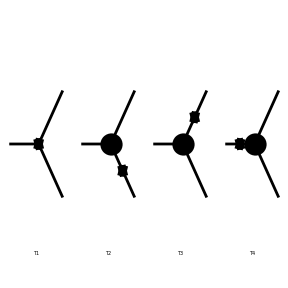

```mathematica
cttops=CreateCTTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->TadpoleCTs];
Paint[cttops];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 4: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 4 Generic, 4 Classes, 4 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

> Top. 2 ad/bdce/ed.m, 0 diagrams

> Top. 3 ad/becd/ed.m, 0 diagrams

> Top. 4 ad/bece/de.m, 0 diagrams

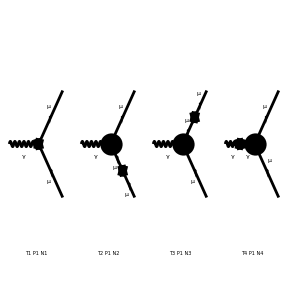

```mathematica
ctins=InsertFields[cttops, process,QEDOnly];
Paint[ctins, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ctamp=CreateFeynAmp[ctins,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 4 Particles amplitudes

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],ⅈ ū[k1,MM].(ⅈ EL (dZAA1/2+dZe1+(dZZA1 (-1/2+SW2))/(2 CW SW)+1/2 dZfL1[2,2,2]^*+1/2 dZfL1[2,2,2]) ga[Lor1].om_-+ⅈ EL (dZAA1/2+dZe1+(dZZA1 SW)/(2 CW)+1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1]],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==2],Integral[],-ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[-(k2)]).(ⅈ (-1/2 MM dZfR1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfL1[2,2,2]) om_-+ⅈ (-1/2 MM dZfL1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfR1[2,2,2]) om_++ⅈ (1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) gs[-(k2)].om_++ⅈ (-1/2 dZfL1[2,2,2]^*-1/2 dZfL1[2,2,2]) gs[k2].om_-).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k2)^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==1,Number==3],Integral[],-ū[k1,MM].(ⅈ (-1/2 MM dZfR1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfL1[2,2,2]) om_-+ⅈ (-1/2 MM dZfL1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfR1[2,2,2]) om_++ⅈ (-1/2 dZfL1[2,2,2]^*-1/2 dZfL1[2,2,2]) gs[-(k1)].om_-+ⅈ (1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) gs[k1].om_+).(MM+gs[k1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k1)^2)],FeynAmp[GraphID[Topology==4,Generic==1,Particles==1,Number==4],Integral[],ū[k1,MM].(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).v[k2,MM] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(k1+k2)^2 (-ⅈ dZAA1 (p1)[Lor2] (-(k1)-k2)[Lor1]+ⅈ dZAA1 g[Lor1,Lor2] (p1).(-(k1)-k2))]]

> Top. 4: 1 Particles amplitude

in total: 4 Particles amplitudes

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],ⅈ ū[k1,MM].(ⅈ EL (dZAA1/2+dZe1+(dZZA1 (-1/2+SW2))/(2 CW SW)+1/2 dZfL1[2,2,2]^*+1/2 dZfL1[2,2,2]) ga[Lor1].om_-+ⅈ EL (dZAA1/2+dZe1+(dZZA1 SW)/(2 CW)+1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1]],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==2],Integral[],-ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[-(k2)]).(ⅈ (-1/2 MM dZfR1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfL1[2,2,2]) om_-+ⅈ (-1/2 MM dZfL1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfR1[2,2,2]) om_++ⅈ (1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) gs[-(k2)].om_++ⅈ (-1/2 dZfL1[2,2,2]^*-1/2 dZfL1[2,2,2]) gs[k2].om_-).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k2)^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==1,Number==3],Integral[],-ū[k1,MM].(ⅈ (-1/2 MM dZfR1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfL1[2,2,2]) om_-+ⅈ (-1/2 MM dZfL1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfR1[2,2,2]) om_++ⅈ (-1/2 dZfL1[2,2,2]^*-1/2 dZfL1[2,2,2]) gs[-(k1)].om_-+ⅈ (1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) gs[k1].om_+).(MM+gs[k1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k1)^2)],FeynAmp[GraphID[Topology==4,Generic==1,Particles==1,Number==4],Integral[],ū[k1,MM].(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).v[k2,MM] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(k1+k2)^2 (-ⅈ dZAA1 (p1)[Lor2] (-(k1)-k2)[Lor1]+ⅈ dZAA1 g[Lor1,Lor2] (p1).(-(k1)-k2))]]

## FormCalc results

```mathematica
ctresult=CalcFeynAmp[ctamp]//Simplify
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/4 EL (Sub12-2 Sub10 Den[MM2,MM2])]

```mathematica
UVDivergentPart[ctresult]
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]

```mathematica
Abbr[]
```

{F3→(u̇ 2|6|v3),F4→(u̇ 2|7|v3),F1→(u̇ 2|6,e[1]|v3),F2→(u̇ 2|7,e[1]|v3),Pair1→Pair[e[1],k[2]]}

```mathematica
Subexpr[]
```

{Sub1→(F1+F2) MM2-(F3+F4) MM Pair1,Sub10→(F1+F2) (Sub2+Sub3)+MM Sub8-2 MM2 Sub9,Sub12→-2 (Sub11+(F2 Sub4)/CW)+(F1 Sub7)/(CW SW),Sub7→dZZA1-2 (Sub6+CW (dZAA1+2 dZe1) SW),Sub11→F1 dZfL1[2,2,2]^*+F2 dZfR1[2,2,2]^*,Sub8→-F2 (MM Sub5-2 dMf1[2,2])+2 (F1+F2) dMf1[2,2]+F1 (MM Sub5+2 dMf1[2,2]),Sub3→2 MM dMf1[2,2]+MM2 dZfL1[2,2,2],Sub6→dZZA1 SW2+CW SW dZfL1[2,2,2],Sub5→dZfL1[2,2,2]-dZfR1[2,2,2],Sub9→F1 dZfL1[2,2,2]+F2 dZfR1[2,2,2],Sub2→2 MM dMf1[2,2]+MM2 dZfR1[2,2,2],Sub4→dZZA1 SW+CW (dZAA1+2 dZe1+dZfR1[2,2,2])}